## Initialization

```mathematica
$FKKSRoot = NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
LogFile = $FKKSRoot<>"Logs/LogFile";
PlotFileExtension = ".png";
NumberofSlaveKernels = Automatic; (*Default should be Automatic*)

(*Import some helper functions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]

(*Setup xAct definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*Setup Proca Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]

(*Setup Energy Momentum Definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "EnergyMomentum.wl"}]]

(*Setup MST Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "MSTSolver.wl"}]]

(*Setup Inhomogeneous Teukolsky Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "TeukolskySolver.wl"}]]
```

```mathematica
data = Import@FileNames["*.mx", NotebookDirectory[]][[2]];
```

```mathematica
Dynamic[$Messenger]
```

```mathematica
Timing[tnnoe = Tnn[data, AsOptimized->True];]
tnnoe[0,100,0.001,0]
```

{65.8085,Null}

1.40508×10^-22

```mathematica
Timing[tnnif = Tnn[data, AsInterpolatingFunction->True];]
tnnif[0,100,0.001,0]
```

{99.1409,Null}

1.30512×10^-16

```mathematica
With[{rsamp = RandomReal[{1.44,100}], thsamp= RandomReal[{0.001,π-0.001}]},
Column[{
rsamp,
thsamp,
(tnnif[0,rsamp,thsamp,0]-tnnoe[0,rsamp,thsamp,0])/tnnoe[0,rsamp,thsamp,0]
}]
]
```

35.158
0.49252
-0.0000115725

```mathematica
ϕsampling = {0, π/(4*data["Parameters", "m"])}
Dmat[phi1_, phi2_] := {{Cos[2*data["Parameters", "m"]*phi1],Sin[2*data["Parameters", "m"]*phi1]},{Cos[2*data["Parameters", "m"]*phi2],Sin[2*data["Parameters", "m"]*phi2]}}
rdom = data["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,data["Parameters", "χ"]]&;
rpoints = 100;
θpoints =50;
CoefficientSolution = LinearSolve[Dmat[Sequence@@ϕsampling], {Aa,Bb}]
reprrule = {Aa->tnnoe[0,r,θ,ϕsampling[[1]]], Bb->tnnoe[0,r,θ,ϕsampling[[2]]]};
```

{0,π/12}

{Aa,Bb}

```mathematica
Timing[
coeff1exp = OptimizedFunction[{r,θ},Evaluate[CoefficientSolution[[1]]/.reprrule], ToCompiled->True, CompilationTarget->"WVM", RuntimeOptions->$TSRuntimeOptions];
coeff2exp =  OptimizedFunction[{r,θ},Evaluate[CoefficientSolution[[2]]/.reprrule], ToCompiled->True, CompilationTarget->"WVM", RuntimeOptions->$TSRuntimeOptions];
]
```

{3.72288,Null}

```mathematica
With[{ωvalue=data["Solution", "ω"]//Re, mvalue = data["Parameters", "m"]},
TnnDecomposedoe = {t,r,θ,ϕ}|->Evaluate[coeff1exp[r,θ]*Cos[-2*ωvalue*t + 2*mvalue*ϕ]+coeff2exp[r,θ]*Sin[-2*ωvalue*t + 2*mvalue*ϕ]]
];
```

```mathematica
With[{rsamp = RandomReal[{1.44,100}], thsamp= RandomReal[{0.001,π-0.001}]},
Column[{
TnnDecomposedoe[0,rsamp,thsamp,0],
tnnoe[0,rsamp,thsamp,0]
}]
]
```

0.000103819+0. ⅈ
0.000103819

```mathematica
Timing[
coeff1 = GenerateInterpolation[coeff1exp[r,θ], {r,rdom[[1]], rdom[[2]],(rdom[[2]]-rdom[[1]])/rpoints}, {θ,θϵ,π-θϵ,π/θpoints}, DensityFunctions->{(#^4&), Identity}];
coeff2= GenerateInterpolation[coeff2exp[r,θ], {r,rdom[[1]], rdom[[2]],(rdom[[2]]-rdom[[1]])/rpoints}, {θ,θϵ,π-θϵ,π/θpoints}, DensityFunctions->{(#^4&), Identity}];
]
```

{14.5107,Null}

```mathematica
With[{rsamp = RandomReal[{1.44,100}], thsamp= RandomReal[{0.001,π-0.001}]},
Column[{
coeff1exp[rsamp,thsamp]-
coeff1[rsamp,thsamp],
coeff2exp[rsamp,thsamp]-
coeff2[rsamp,thsamp]
}]
]
```

2.30026×10^-14+0. ⅈ
3.26222×10^-14+0. ⅈ

```mathematica
With[{ωvalue=data["Solution", "ω"]//Re, mvalue = data["Parameters", "m"]},
TnnDecomposed = {t,r,θ,ϕ}|->Evaluate[coeff1[r,θ]*Cos[-2*ωvalue*t + 2*mvalue*ϕ]+coeff2[r,θ]*Sin[-2*ωvalue*t + 2*mvalue*ϕ]]
];
```

```mathematica
With[{rsamp = RandomReal[{1.44,100}], thsamp= RandomReal[{0.001,π-0.001}]},
Column[{
rsamp,
thsamp,
(TnnDecomposed[0,rsamp,thsamp,0]-tnnoe[0,rsamp,thsamp,0])/tnnoe[0,rsamp,thsamp,0]
}]
]
```

84.8378
0.873227
-0.00294003

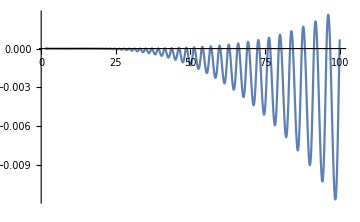
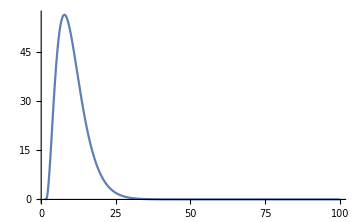
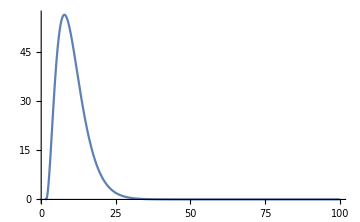

```mathematica
Row[{
Plot[
(TnnDecomposed[0,r,π/4,0]-tnnoe[0,r,π/4,0])/tnnoe[0,r,π/4,0], {r,1.44,100},ImageSize->Medium, PlotRange->All],
Plot[TnnDecomposed[0,r,π/4,0], {r,1.44,100},ImageSize->Medium, PlotRange->All],
Plot[tnnoe[0,r,π/4,0], {r,1.44,100},ImageSize->Medium, PlotRange->All]
}]
```

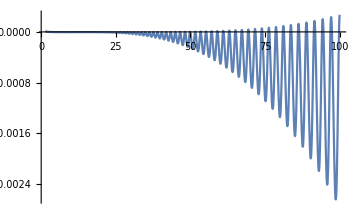
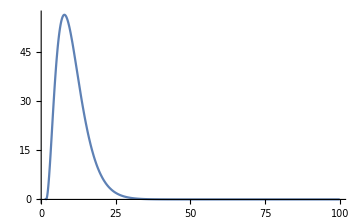
-Graphics--Graphics--Graphics-

```mathematica
Row[{
Plot[
(tnnif[0,r,π/4,0]-tnnoe[0,r,π/4,0])/tnnoe[0,r,π/4,0], {r,1.44,100},ImageSize->Medium, PlotRange->All],
Plot[tnnif[0,r,π/4,0], {r,1.44,100},ImageSize->Medium, PlotRange->All],
Plot[tnnoe[0,r,π/4,0], {r,1.44,100},ImageSize->Medium, PlotRange->All]
}]
```

```mathematica
tmp = Import[FileNameJoin[{$FKKSRoot, "Expressions", "FKKSEnergyMomentumNN.mx"}]];
```

```mathematica
Timing[tmp1 = tmp/.ToParamSymbols;]
Timing[tmp2 = tmp1/.ωi->0;]
Timing[tmp3 = tmp2//FromxActVariables;]
Timing[tmp4 = tmp3//ApplyRealSolutionSet[data];]
```

```mathematica
oec = OptimizedFunction[{t,r,θ,ϕ}, tmp4, ToCompiled->True, CompilationTarget->"WVM", RuntimeOptions->{"CatchMachineOverflow"->False, "CatchMachineIntegerOverflow"->False, "CompareWithTolerance"->False, "EvaluateSymbolically"->False, "RuntimeErrorHandler"->Null, "WarningMessages"->True}];
oe = OptimizedFunction[{t,r,θ,ϕ}, tmp4];
```

```mathematica
oec[0,2,RandomReal[{0,π}],0]//Timing
oe[0,2,RandomReal[{0,π}],0]//Timing
ClearSystemCache[]
```

```mathematica
tnn =
```

```mathematica
DateString[]
```

```mathematica
dat = Import/@FileNames[All, "/home/shaunf/ITPCluster_DataStore/KerrDressedWithProca/Solutions/"];
```

```mathematica
datDerived = Select[dat, KeyExistsQ[#,"Derived"]&];
```

```mathematica
μvs = datDerived[[All, "Parameters", "μNv"]];
ωvs = datDerived[[All, "Solution", "ω"]];
Einf = datDerived[[All, "Derived", "Einf"]];
```

```mathematica
ListLogPlot[Thread[{Im[ωvs], Einf}]]
```

```mathematica
datDerived[[All, "Derived"]]
```

```mathematica
dat = getResults[$SolutionPath];
```

```mathematica
indexer=Ordering@Table[dat[[i, "Solution", "R"]]["Domain"]//Last, {i,1,Length@dat}];
dat = dat[[indexer]];
```

```mathematica
Dynamic[$Messenger]
```

```mathematica
Block[{},
Timer = Timing[(Tlmw= TeukolskySourceModal[dat[[-1]],2,2]);]
];
```

```mathematica
dat[[1]]
```

```mathematica
Timess300
Plot[Tlmw300[r]//Re, {r,1.44,30000}]
```

```mathematica
Plot[10*Log[x], {x,1,50000}]
```

```mathematica
Timess200
Plot[Tlmw200[r]//Re, {r,1.44,200}]
```

```mathematica
Timess100
Plot[Tlmw100[r]//Re, {r,1.44,8000}]
```

```mathematica
NIntegrate[Tlmw100[r], {r,1.44,8000}]
NIntegrate[Tlmw200[r], {r,1.44,8000}]
NIntegrate[Tlmw300[r], {r,1.44,8000}]
```

```mathematica
Thread[{Last[First[#["Domain"]]]&/@Tlmws,Timess[[All,1]]}]//ListPlot
```

```mathematica
Unprotect[CellPrint];
CellPrint[Cell[s_, "Print", label_, ShowCellLabel->True]]:=Block[{},
CellPrint[Cell[s,"Print",ShowCellLabel->False]]];
Protect[CellPrint];
ParallelEvaluate[Print["Test"]];
```

```mathematica
Trace[ParallelEvaluate[Print["d"]], CellPrint]//Flatten
```

```mathematica
Block[{},DiffAtHorizon = Series[ProcaDiffOpRad@R[r]//Simplify, {r,1+Sqrt[1-χ^2],1}]//Normal];
```

```mathematica
DiffAtHorizon/.R[_]:>R[r]/.Derivative[x_][R][_]:>Derivative[x][R][r]//Simplify
```

```mathematica
(Collect[diff//Expand, {R[r],Derivative[_][R][_]}]/.c1_*R[r]+c2_*Derivative[1][R][r]+c3_*Derivative[2][R][r]->{c1,c2,c3})/((1+r^2*ν^2)/((-1+r-√(1-χ^2)) (-1+r+√(1-χ^2))));
Series[%, {r, 1+Sqrt[1-χ^2],1}]//Normal//Simplify;
ODEAtHorizon = Sum[%[[i+1]]*Derivative[i][R][r], {i,0,2}];
SolutionAtHorizon = R[r]/.DSolve[ODEAtHorizon==0,R,r]//First;
```

```mathematica
SolutionAtHorizon//Simplify
```

```mathematica
ReorganizedODE = Collect[DiffAtHorizon//Expand, {R[r], Derivative[1][R][r], Derivative[2][R][r]}];
ODECoefficients = (ReorganizedODE/.c1_*R[r]+c2_*Derivative[1][R][r]+c3_*Derivative[2][R][r]->{c1,c2,c3})/((1+r^2*ν^2)/((-1+r-√(1-χ^2)) (-1+r+√(1-χ^2))))//FullSimplify
ODECoefficientHorizon = Series[ODECoefficients, {r,1+Sqrt[1-χ^2],1}]//Normal//Simplify
ODEAtHorizon = Sum[ODECoefficientHorizon[[i+1]]*Derivative[i][R][r], {i,0,2}];
SolutionAtHorizon = R[r]/.DSolve[ODEAtHorizon==0,R,r]//First;
(Series[SolutionAtHorizon, {r,∞,1}]//Normal)/.Times[x_,y_,z_]->x*y
```

```mathematica
nmin = 0; nmax =  4; mmin= 1; mmax= 4;
AllProcaSolutions = getResults[$SolutionPath];
μOrderingIndex = Ordering@AllProcaSolutions[[All, "Parameters", "μNv"]];
AllProcaSolutions = AllProcaSolutions[[μOrderingIndex]];
ReDataCollection = Association@@(Table[
(ωvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Solution", "ω"]];
μvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Parameters", "μNv"]];
"n"<>ToString[ni]<>"m"<>ToString[mi]-> Thread[{μvs, Re@ωvs}]
), {ni, nmin,nmax}, {mi, mmin,mmax}]//Flatten[#,1]&);
ImDataCollection = Association@@(Table[
(ωvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Solution", "ω"]];
μvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Parameters", "μNv"]];
"n"<>ToString[ni]<>"m"<>ToString[mi]-> Thread[{μvs, Im@ωvs}]
), {ni, nmin,nmax}, {mi, mmin,mmax}]//Flatten[#,1]&);
```

```mathematica
sol = getResults[$SolutionPath, {{"m",3},{"n",0}, {"μNv", "51_50"}}]//First;
actualinterp = omegaFit[30]/.sol[["Solution", "ωfit"]];
```

```mathematica
AnnotationKeys[actualinterp];
domain = actualinterp["Coordinates"]//First;
range = actualinterp["ValuesOnGrid"];
testinterp  =Interpolation[Thread[{domain, range}], InterpolationOrder->3];
```

```mathematica
ClearAll[dat,dat1]
dat1 = DataCollection["n0m3"];
Manipulate[
dom = dat1[[i;;i+5]][[All,1]];
interp = Interpolation[dat1[[i;;i+5]], Method->"Hermite"];
Show[{
ListLogPlot[dat1],
ListLogPlot[{dat1[[i+6]]}, PlotMarkers->"⊗"],
LogPlot[interp[j], {j,dom[[1]], dom[[-1]]+3/100}]
(*LogPlot[Im[actualinterp[j]],{j,dom[[1]], dom[[-1]]+3/100}],
LogPlot[Im[testinterp[j]],{j,dom[[1]], dom[[-1]]+3/100}]*)
}, PlotRange->{{dom[[1]],dom[[-1]]+6/100}, {All, All}}],
{i,20,25,1}
]
```

```mathematica
ttest = {}
param = {0,2,0.1};
Do[AppendTo[ttest,-(i-1)^2]; If[i>3,If[ttest[[-2]]>ttest[[-1]], param[[3]]=0.01]]
, {i,0,2,0.1}]
ttest
```

```mathematica
parameters["μrange"] = {0.05,0.5};
parameters["δμ"]=5/100;
parameters["m"]=3;
```

```mathematica
MassMesh = Table[i, {i,parameters["μrange"][[1]], parameters["μrange"][[-1]]*parameters["m"], parameters["δμ"]}]
```

```mathematica
3*KerrSurfaceRotationN[0.9]
```

```mathematica
Graphics[Line[{{3*KerrSurfaceRotationN[0.9],0},{3*KerrSurfaceRotationN[0.9],1}}], Frame->True]
```

```mathematica
Show[{
ImDataCollection["n4m1"]//ListLogPlot,
Graphics[Line[1.2*4*{{KerrSurfaceRotationN[0.9],-100},{KerrSurfaceRotationN[0.9],1}}], Frame->True]
}]
```

```mathematica
omegaNRNonRel[<|"χ"->0.9, "μNv"->x, "m"->3, "n"->0, "l"->2, "s"->-1|>]/3<KerrSurfaceRotationN[0.9]
Reduce[%,x]
```

```mathematica
omegaNINonRel[<|"χ"->9/10, "μNv"->x, "m"->3, "n"->0, "l"->2, "s"->-1|>]//FullSimplify
```

```mathematica
Show[
Plot[omegaNINonRel[<|"χ"->0.9, "μNv"->x, "m"->3, "n"->0, "l"->2, "s"->-1|>], {x,.05,1}],Graphics@Line[{{3*KerrSurfaceRotationN[0.9],-100},{3*KerrSurfaceRotationN[0.9],1}}]]
```

```mathematica
AllProcaSolutions = getResults[$SolutionPath];
μOrderingIndex = Ordering@AllProcaSolutions[[All, "Parameters", "μNv"]];
AllProcaSolutions = AllProcaSolutions[[μOrderingIndex]];
```

```mathematica
ωvs = OvertoneModeGroup[0,1,AllProcaSolutions][[All, "Solution", "ω"]];
νvs = OvertoneModeGroup[0,1,AllProcaSolutions][[All, "Solution", "ν"]];
μvs = OvertoneModeGroup[0,1,AllProcaSolutions][[All, "Parameters", "μNv"]];
imdat = Thread[{μvs, Im@ωvs}];
redat = Thread[{μvs, (Re@ωvs)/μvs}];
```

```mathematica
Manipulate[
With[{i=j},
interp = Interpolation[imdat[[i;;i+5]], InterpolationOrder->3];
Show[{
ListLogPlot[imdat[[1;;30+5]]],
LogPlot[interp[zeta], {zeta,4/100+i/100,12/100+i/100}]
}]
],
{j,1,30}
]
```

```mathematica
interp[0.3]
```

```mathematica
$HistoryLength=4;
Unprotect[Debug];
```

## Setup

```mathematica
<<KerrWithProca`
```

```mathematica
$FKKSRoot = "/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/Mathematica/"
(*Import Proca Mode Solver*)
<<KerrWithProca`
(*Import xAct Setup*)
Get[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*$Assumptions={r>0,M>0,J>0,1>a≥0,π≥θ≥0, λ∈Complexes,ω∈Complexes, ν∈Complexes};*)

M=1;
SolutionPath =$FKKSRoot<>"Solutions/";
AnalyticSolution = <|"Parameters"-><|"ϵ"->ϵ,"μNv"->μNv,"m"->m,"n"->n,"χ"->χ,"M"->M|>,"Solution"-><|"ω"->ω,"ν"->ν,"R"->R,"S"->S|>|>;
```

## Helper Functions

```mathematica
OvertoneModeGroup[nvalue_?NumberQ, mvalue_?NumberQ]:=Select[Select[AllSolutions, #["Parameters"]["n"]==nvalue&], #["Parameters"]["m"]==mvalue&]

HorizonCoordToRadial[xN_, χ_]:=xN * (rplusN[χ] - rminusN[χ])  +  rplusN[χ];
RadialToHorizonCoord[rN_,χ_]:=(rN - rplusN[χ])/(rplusN[χ] - rminusN[χ]);

(*https://mathematica.stackexchange.com/questions/59944/extracting-the-function-from-interpolatingfunction-object/59963#59963*)
InterpolationToPiecewise[if_,x_]:=Module[{main,default,grid},grid=if["Grid"];
Piecewise[{if@"GetPolynomial"[#,x-#],x<First@#}&/@grid[[2;;-2]],if@"GetPolynomial"[#,x-#]&@grid[[-1]]]]/;if["InterpolationMethod"]=="Hermite"

CompileInterpolating[interp_InterpolatingFunction]:=Compile[{ψ}, Evaluate[InterpolationToPiecewise[interp, ψ]]]

ParamsToReprRule[solution_]:=AssociationThread[(Symbol/@(solution[ "Parameters"]//Keys))->(solution[ "Parameters"]//Values)]//Normal

ToRational[expr_]:=Rationalize[expr,0]
PrimedToSymbolic[expr_]:=expr/.{R''->ddR, R'->dR};

SolToReprRule[solution_,OptionsPattern[{real->False}]]:=
With[{ωv = solution["Solution","ω"],νv = solution["Solution","ν"], Rv=solution["Solution","R"], Sv = solution["Solution","S"], χv = solution["Parameters","χ"]},
If[OptionValue[real],
AssociationThread[{ω,ν,S,R,dR,ddR}->Flatten@{Re[ωv],
											νv,
											Sv,
											(Rv[RadialToHorizonCoord[#,χv]]&), 
											((Rv'[RadialToHorizonCoord[#,χv]]*1/(rplusN[χv]-rminusN[χv]))&),
											((Rv''[RadialToHorizonCoord[#,χv]]*1/(rplusN[χv]-rminusN[χv])^2)&)
}
],

AssociationThread[{ω,ν,S,R,dR,ddR}->Flatten@{ωv,
											νv,
											Sv,
											(Rv[RadialToHorizonCoord[#,χv]]&), 
											((Rv'[RadialToHorizonCoord[#,χv]]*1/(rplusN[χv]-rminusN[χv]))&),
											((Rv''[RadialToHorizonCoord[#,χv]]*1/(rplusN[χv]-rminusN[χv])^2)&)
}
](*Dont forgot to convert radial function from horizon co-ordinates to Boyer-Lindquist radial coordinates! Polarization tensor is in terms of radial coordinates, so we must match the arguments for the Z fkks function.*)
]
];


ToParamSymbols:={a->χ, λ->1/ν};

ApplySolutionSet[solution_,OptionsPattern[{real->False}]][expr_]:= expr/.ToParamSymbols/.ParamsToReprRule[solution]/.SolToReprRule[solution,real->OptionValue[real]];

OptimizedFunction[vars_, expr_]:=Block[{tmpOE,res},
tmpOE = Experimental`OptimizeExpression[expr, OptimizationSymbol->a];
tmpOE/.Experimental`OptimizedExpression[f_]:>Function@@Hold[vars, f]
]

DetMet[r_,θ_,χ_]:= -(r^2+χ^2*Cos[θ]^2)^2*Sin[θ]^2

ErgoRadius[θ_,χ_, OptionsPattern[{coords->BL}]]:=
If[TrueQ[OptionValue[coords]==BL],1+Sqrt[1-χ^2*Cos[θ]^2],
If[TrueQ[OptionValue[coords]==Horizon],RadialToHorizonCoord[1+Sqrt[1-χ^2*Cos[θ]^2],χ],
Print["Coords must be either BL (boyer-lindquist) or Horizon"]
]
];
```

## Calculations

```mathematica
analytic;
FKKSProca[solution_:analytic, OptionsPattern[{SymbolicExpression->False, Optimized->False}]]:=
Block[{res,tmp,gradZ,Z},
With[{ProcaFilePath = $FKKSRoot<>"Expressions/FKKSProcaCTensor.mx"},
If[
FileExistsQ[ProcaFilePath],
res = Import[ProcaFilePath];,
Z = R[r[]]*S[θ[]]*Exp[-I*ω*t[]]*Exp[I*m*ϕ[]];
res = Head[Polarization[ζ,ξ]Cd[-ξ]@Z//FromBasisExpand//Simplify];
Export[ProcaFilePath,res];
]
];
If[TrueQ[solution==analytic],
Return[res/.ToParamSymbols]
];

tmp = res//FromxActVariables//PrimedToSymbolic//ApplySolutionSet[solution];
If[OptionValue[SymbolicExpression], 
Return[tmp]
];

If[OptionValue[Optimized],
Return[OptimizedFunction[{t,r,θ,ϕ}, Evaluate[tmp]]]
];

Return[{t,r,θ,ϕ}|->Evaluate[tmp]]
]

FKKSProcaNorm[solution_:analytic,OptionsPattern[{SymbolicExpression->False, Optimized->False}]]:=
Block[{tmp,res,A},
With[{FSFilePath = $FKKSRoot<>"Expressions/FKKSProcaNorm.mx"},
If[
FileExistsQ[FSFilePath],
res = Import[FSFilePath];,

A=FKKSProca[analytic];
res = A[-ζ]A[ζ];
Export[FSFilePath, res];
]
];
(*Format output based on input arguments*)
If[TrueQ[solution==analytic],
Return[res/.ToParamSymbols]
];
tmp = res//FromxActVariables//PrimedToSymbolic//ApplySolutionSet[solution];

If[OptionValue[SymbolicExpression], 
Return[tmp]
];

If[OptionValue[Optimized],
Return[OptimizedFunction[{t,r,θ,ϕ}, Evaluate[tmp]]]
];

Return[{t,r,θ,ϕ}|->Evaluate[tmp]]
]


FKKSFieldStrength[solution_, OptionsPattern[{SymbolicExpression->False, Optimized->False}]]:=
Block[{res,tmp,A},

With[{FSFilePath = $FKKSRoot<>"Expressions/FKKSFieldStrengthCTensor.mx"},
If[
FileExistsQ[FSFilePath],
res = Import[FSFilePath];,
A=FKKSProca[analytic];
res = Head[Cd[-ζ]@A[-ξ] - Cd[-ξ]@A[-ζ]];
Export[FSFilePath, res];
]
];
(*Format output based on input arguments*)
If[TrueQ[solution==analytic],
Return[res/.ToParamSymbols]
];
tmp = res//FromxActVariables//PrimedToSymbolic//ApplySolutionSet[solution];

If[OptionValue[SymbolicExpression], 
Return[tmp]
];

If[OptionValue[Optimized],
Return[OptimizedFunction[{t,r,θ,ϕ}, Evaluate[tmp]]]
];

Return[{t,r,θ,ϕ}|->Evaluate[tmp]]
]


FKKSEnergyMomentum[solution_, OptionsPattern[{SymbolicExpression->False, Debug->False, Optimized->False}]]:=
Block[{res,tmp,tmp$, mass = μNv, tmpOE,F,A},
With[{EMFilePath = $FKKSRoot<>"Expressions/FKKSEnergyMomentumCTensor.mx"},
If[
FileExistsQ[EMFilePath],
res = Import[EMFilePath];,

F = FKKSFieldStrength[analytic];
A=FKKSProca[analytic];
tmp$ = F[-ζ,-γ]F[-ξ,γ] + mass^2*A[-ζ]A[-ξ] -1/4 met[-ζ,-ξ](F[-ι,-γ]F[ι,γ] + 2*mass^2*A[-γ]A[γ]);
res=Evaluate@Head[tmp$];
If[TrueQ[Head[res]!=CTensor],Print["ERROR: Form of EM tensor incorrect"],Export[EMFilePath,res]];
]
];
(*Format output based on input arguments*)
If[TrueQ[solution==analytic],
Return[res/.ToParamSymbols]
];
tmp = res//FromxActVariables//PrimedToSymbolic//ApplySolutionSet[solution,real->True];

If[OptionValue[SymbolicExpression], 
Return[tmp]
];

If[OptionValue[Optimized],
Return[OptimizedFunction[{t,r,θ,ϕ}, Evaluate[tmp]]]
];

Return[{t,r,θ,ϕ}|->Evaluate[tmp]]

]


FKKSEnergyDensity[solution_, OptionsPattern[{SymbolicExpression->False,Optimized->True, }]]:=
Block[{res, resOE,T,OptimizedResult, tmp,UnOptimizedResult},

With[{ENFilePath =$FKKSRoot<>"Expressions/FKKSEnergyDensity.mx"},
If[FileExistsQ[ENFilePath],
res = Import[ENFilePath];,

T = FKKSEnergyMomentum[analytic];
res = -1*T[{0,sphericalchart},{0,-sphericalchart}]//FromxActVariables;
Export[ENFilePath, res];
];
];
(*Format output based on input arguments*)
If[TrueQ[solution==analytic],
Return[res/.ToParamSymbols]
];
tmp = res//FromxActVariables//PrimedToSymbolic//ApplySolutionSet[solution,real->True];

If[OptionValue[SymbolicExpression], 
Return[tmp]
];

If[OptionValue[Optimized],
Return[OptimizedFunction[{t,r,θ,ϕ}, Evaluate[tmp]]]
];

Return[{t,r,θ,ϕ}|->Evaluate[tmp]]
]


FKKSEnergyMomentumTrace[solution_, OptionsPattern[{SymbolicExpression->False,Optimized->True, }]]:=
Block[{res, resOE,fkksEM,OptimizedResult, tmp},

With[{ENFilePath =$FKKSRoot<>"Expressions/FKKSEnergyMomentumTrace.mx"},
If[FileExistsQ[ENFilePath],
res = Import[ENFilePath];,
fkksEM = FKKSEnergyMomentum[analytic];
res = fkksEM[{ζ,sphericalchart},{ξ,sphericalchart}]met[{-ζ,-sphericalchart},{-ξ,-sphericalchart}]//TraceBasisDummy;
Export[ENFilePath, res];
];
];
(*Format output based on input arguments*)
If[TrueQ[solution==analytic],
Return[res/.ToParamSymbols]
];
tmp = res//FromxActVariables//PrimedToSymbolic//ApplySolutionSet[solution,real->True];

If[OptionValue[SymbolicExpression], 
Return[tmp]
];

If[OptionValue[Optimized],
Return[OptimizedFunction[{t,r,θ,ϕ}, Evaluate[tmp]]]
];

Return[{t,r,θ,ϕ}|->Evaluate[tmp]]
]


FinalDimlessSpin[InitialDimlessSpin_,freq_,mode_,MInitial_,MRatio_]:=mode/freq*1/MInitial*(1-1/MRatio)+InitialDimlessSpin/MRatio;

SaturationCondition::usage="Condition that must be satisfied for superradiant amplification to cease. Condition is satisfied when this function equals 0.
ω/m-χ_f/(2 SubscriptBox[M, f] (1 - √(1 - SuperscriptBox[SubscriptBox[χ, f], 2])))=0";
SaturationCondition[freq_,mode_,InitialDimlessSpin_,MInitial_,MRatio_]:=
Block[{chiFinal = FinalDimlessSpin[InitialDimlessSpin,freq,mode,MInitial,MRatio]},
freq/mode-chiFinal/(2*MRatio*MInitial*(1+Sqrt[1-chiFinal^2]))
]

FinalMass[freq_,mode_,InitialDimlessSpin_,MInitial_]:=
Block[{mm},mm/.NSolve[SaturationCondition[freq,mode,InitialDimlessSpin,MInitial,mm],mm,Reals] ]
```

```mathematica
nilsres = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/precision_mode_library/m1n0_a900000_Sm1_prec_p_HPee.mx"];
nilsR = Function[{r},nilsres[[-2]][[1]][[1]][[2]][HorizonCoordToRadial[r,0.9]]];
nilsS = {θ}|->nilsres[[-6]][[1]]/.QNMcode`θ->θ//Evaluate;
nilsw = nilsres[[-3]][[1]];
nilsn = QNMcode`rν+I*QNMcode`iν/.nilsres[[-4]][[1]];
nilsm = nilsres[[-5]][[1]];
nilssol = <|"Solution"-><|"R"->nilsR, "S"->nilsS, "ω"->nilsw, "ν"->nilsn|>, "Parameters"-><|"m"->1, "n"->0,  "χ"->0.9, "μNv"->nilsm, "M"->1, "ϵ"->0.0001|>
|>;
Plot3D[nilssol["Solution","R"][r]*nilssol["Solution","S"][θ]//Re, {r,1.436,1000},{θ,0,π}, PlotRange->All];
Plot[nilssol["Solution","S"]'[t]//Re, {t,0,π}];
Plot[nilssol["Solution","R"][t]//Re, {t,01.436,3000}]
```

```mathematica
dolanR = InterpolatingFunction[…];
dolanχ = 0.99;
dolanm = 1;
dolans = -1;
dolanμ = 0.4;
dolanω = 0.35920565365675217+0.0002369433184210433 ⅈ;
dolanν = -0.6002837284375238-0.00033368731882264666 ⅈ;
dolansol = <|"Solution"-><|"R"->dolanR, "S"->nilsS, "ω"->dolanω, "ν"->dolanν|>, "Parameters"-><|"m"->dolanm, "n"->0,  "χ"->dolanχ, "μNv"->dolanμ, "M"->1, "ϵ"->0.0001|>
|>;
```

```mathematica
testsol1 = getResults[SolutionPath,{{"χ","9_10"},{"m","1"},{"n","0"}, {"μNv","2_5"}}][[2]];
testsol2= getResults[SolutionPath,{{"χ","9_10"},{"m","1"},{"n","0"}, {"μNv","11_100"}}][[3]];
testsol1["Solution","R"]=testsol1["Solution","R(r)"];
testsol1["Solution","S"]={θ}|->10*testsol1["Solution","S(θ)"][θ];
testsol2["Solution","R"]=testsol2["Solution","R(r)"];
testsol2["Solution","S"]=nilsS;(*testsol2["Solution","S(θ)"];*)
rdom = testsol1[["Solution", "R"]]["Domain"]//First//Last//HorizonCoordToRadial[#,testsol1[["Parameters","χ"]]]&;
r1dom = testsol2[["Solution", "R"]]["Domain"]//First//Last//HorizonCoordToRadial[#,testsol2[["Parameters","χ"]]]&;
Plot3D[testsol2["Solution","R"][r]*testsol2["Solution","S"][θ]//Re, {r,1.436,1000},{θ,0,π}, PlotRange->All];
Plot[(testsol2["Solution","S"][t]-testsol1["Solution","S"][t])//Re, {t,0,π}];
Plot[(testsol2["Solution","R"][t])//Re, {t,1.436,2000}, PlotRange->All];
```

```mathematica
(*testsol = dolansol;*)
testsol = testsol2;
```

```mathematica
TudNils = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/Tud.mx"];
TddNils = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/Tdd.mx"];
coordinates={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};
coordconv={Global`t->t,Global`r->r,Global`θ->θ,Global`ϕ->ϕ};
coordrev={t->Private`t,r->Private`r,θ->Private`θ,ϕ->Private`ϕ};
AupSimp=Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/AupSimp.mx"]//.coordinates//.coordconv;
AdownSimp=Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/AdownSimp.mx"]//.coordinates//.coordconv;
```

```mathematica
proca = FKKSProca[nilssol][t,r,θ,ϕ];
Arepr = Table[ToExpression["A"<>ToString[i]]->proca[{i,sphericalchart}], {i,0,3}];
DArepr = Flatten@Table[ToExpression["D"<>ToString[i]<>"A"<>ToString[k]]->D[proca[{k,-sphericalchart}],{t,r,θ,ϕ}[[i+1]]],{i,0,3},{k,0,3}];
```

```mathematica
enme = FKKSEnergyDensity[testsol];
enden = TudNils[[1,1]]/.Private`χ->χ//FromxActVariables;
endentest = OptimizedFunction[{t,r,θ,ϕ},Evaluate[((enden//FromxActVariables)//.DArepr//.Arepr//FromxActVariables)/.μ->testsol["Parameters","μNv"]/.χ->testsol["Parameters","χ"]/.Global`a->testsol["Parameters","χ"]]];
```

```mathematica
Rad = testsol["Solution","R"];
dRad = testsol["Solution","R"]';
ddRad = testsol["Solution","R"]'';
Sangl = testsol["Solution","S"];
dSangl = testsol["Solution","S"]';
ddSangl = testsol["Solution","S"]'';
solidentify={Ri[r_]:>Im[Rad[r]],Rr[r_]:>Re[Rad[r]],Ri'[r_]:>Im[dRad[r]],Rr'[r_]:>Re[dRad[r]],Rr''[r_]:>Re[ddRad[r]],Ri''[r_]:>Im[ddRad[r]],Si[θ_]:>Im[Sangl[θ]],Sr[θ_]:>Re[Sangl[θ]],Si'[θ_]:>Im[dSangl[θ]],Sr'[θ_]:>Re[dSangl[θ]],Sr''[θ_]:>Re[ddSangl[θ]],Si''[θ_]:>Im[ddSangl[θ]]};
```

```mathematica
prec = SetPrecision[#,$MachinePrecision]&;
parameters={χ->0.9,m->1,rν->Re@testsol["Solution","ν"],iν->Im@testsol["Solution","ν"],ωi->0,ωr->Re@testsol["Solution","ω"],μ->testsol["Parameters","μNv"],nh->testsol["Parameters","n"]};
```

```mathematica
eval[A_]:=A//ToBasis[ch]//ComponentArray//ToBasis[ch]//TraceBasisDummy//ToValues//Simplify
Tdd=TddNils//.coordinates//.{Global`m->m,Global`ωr->ωr,Global`ωi->ωi,Global`χ->χ,Global`rν->rν,Global`iν->iν,Global`Si->Si,Global`Ri->Ri,Global`Sr->Sr,Global`Rr->Rr}//.coordconv;
edenrule={Table[ToExpression["Global`D"<>ToString[i]<>ToString["A"]<>ToString[k]]->ToExpression["D"<>ToString[i]<>ToString["A"]<>ToString[k]],{i,0,3},{k,0,3}],Table[ToExpression["Global`A"<>ToString[i]]->ToExpression["A"<>ToString[i]],{i,0,3}]}//Flatten;
edenrule1={Table[ToExpression["Private`D"<>ToString[i]<>ToString["A"]<>ToString[k]]->ToExpression["D"<>ToString[i]<>ToString["A"]<>ToString[k]],{i,0,3},{k,0,3}],Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]],{i,0,3}]}//Flatten;
Tud=TudNils//.coordinates//.{Global`m->m,Global`ωr->ωr,Global`ωi->ωi,Global`χ->χ,Global`rν->rν,Global`iν->iν,Global`Si->Si,Global`Ri->Ri,Global`Sr->Sr,Global`Rr->Rr, Private`χ->χ}//.coordconv;
Tudtemp=enden//.edenrule/.edenrule1/.{t->t,r->r,θ->θ,ϕ->ϕ};
```

```mathematica
coefflistdown=DeleteCases[CoefficientList[AdownSimp[[1]]/.{ωi->0},{sin,cos}]/.{νi->iν,νr->rν}/.parameters,0,2]//Flatten;
coefflistup=DeleteCases[CoefficientList[AupSimp[[1]]/.{ωi->0},{sin,cos}]/.{νi->iν,νr->rν}/.parameters,0,2]//Flatten;
```

```mathematica
ClearAll[rad,sag, Radr, Radi, Sagr, Sagi, dRr, dRi, dSr, dSi, ddRr, ddRi, ddSr, ddSi, Ri, Rr, Si, Sr];
rad = testsol["Solution","R"];
sag = testsol["Solution","S"];
Radr = Evaluate[(Re[rad[#]]&)];
Radi = Evaluate[(Im[rad[#]]&)];
Sagr = Evaluate[(Re[sag[#]]&)];
Sagi = Evaluate[(Im[sag[#]]&)];
dRr = Evaluate[(Re[rad'[#]]&)];
dRi = Evaluate[(Im[rad'[#]]&)];
dSr = Evaluate[(Re[sag'[#]]&)];
dSi = Evaluate[(Im[sag'[#]]&)];
ddRr = Evaluate[(Re[rad''[#]]&)];
ddRi = Evaluate[(Im[rad''[#]]&)];
ddSr = Evaluate[(Re[sag''[#]]&)];
ddSi = Evaluate[(Im[sag''[#]]&)];
ddsolrepr = {Ri''->ddRi,Rr''->ddRr,Si''->ddSi,Sr''->ddSr};
dsolrepr = {Ri'->dRi,Rr'->dRr,Si'->dSi,Sr'->dSr};
solrepr = {Rr->Radr, Ri->Radi, Si->Sagi,Sr->Sagr};
```

```mathematica
Asol = AdownSimp/.ddsolrepr/.dsolrepr/.solrepr/.parameters;
```

```mathematica
Asoloe = OptimizedFunction[{t,r,θ,ϕ},Asol];
```

```mathematica
eval[A_]:=A//ToBasis[ch]//ComponentArray//ToBasis[ch]//TraceBasisDummy//ToValues//Simplify
edenrule={Table[ToExpression["Global`D"<>ToString[i]<>ToString["A"]<>ToString[k]]->ToExpression["D"<>ToString[i]<>ToString["A"]<>ToString[k]],{i,0,3},{k,0,3}],Table[ToExpression["Global`A"<>ToString[i]]->ToExpression["A"<>ToString[i]],{i,0,3}]}//Flatten;
edenrule1={Table[ToExpression["Private`D"<>ToString[i]<>ToString["A"]<>ToString[k]]->ToExpression["D"<>ToString[i]<>ToString["A"]<>ToString[k]],{i,0,3},{k,0,3}],Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]],{i,0,3}]}//Flatten;
Tudtemp=Tud[[1,1]]//.edenrule/.edenrule1/.{t->t,r->r,θ->θ,ϕ->ϕ};
```

```mathematica
(*Integrating over the spatial 3-slice outside of the horizon for the complete mass*)
Aexpl=Table[{ToExpression["A"<>ToString[i]]->Asoloe[t,r,θ,ϕ][[i+1]]},{i,0,3}]/.Im'[x_]->1/.Re'[x_]->1//Flatten;
dAexpl=Table[{ToExpression["D"<>ToString[i]<>ToString["A"]<>ToString[k]]->D[Asoloe[t,r,θ,ϕ][[k+1]],{t,r,θ,ϕ}[[i+1]]]},{i,0,3},{k,0,3}]/.Im'[x_]->1/.Re'[x_]->1//Flatten;
```

```mathematica
TuptdowntTEMP=(Tudtemp/.{ωi->0}/.parameters)/.Aexpl/.dAexpl/.coordinates;
```

```mathematica
Tuptdownt=OptimizedFunction[{t,r,θ,ϕ},TuptdowntTEMP];
```

```mathematica
endenNils=OptimizedFunction[{t,r,θ,ϕ},-Tuptdownt[t,r,θ,ϕ]];
```

```mathematica
Plot3D[Sin[θ]*(r^2+0.9^2*Cos[θ]^2)endenNils[0,r,θ,0]//Re,{r,1.436,1000},{θ,0.01,π-0.01}, PlotRange->{0,All}, RegionFunction->Function[{r,θ}, r>1+Sqrt[1-0.9^2*Cos[θ]^2]], PlotPoints->10, MaxRecursion->1]
```

```mathematica
nilsen = FKKSEnergyDensity[testsol];
```

```mathematica
Plot3D[Sin[θ]*(r^2+0.9^2*Cos[θ]^2)nilsen[0,r,θ,0]//Re,{r,1.436,2},{θ,0.1,π-0.1}, PlotRange->{All,All}, RegionFunction->Function[{r,θ}, r>1+Sqrt[1-0.9^2*Cos[θ]^2]]]
```